## Calculations for 2 and ∞ norms (Problem 9.10)

```mathematica
Clear["Global`*"];
```

For 2nd-order system

```mathematica
g=1/(1+2 ζ s + s^2); gtf = TransferFunctionModel[g,s]; gss=StateSpaceModel[gtf]
pinf=ControllabilityGramian[gss]; TraditionalForm[pinf]
```

010-1-2 ζ1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

(1/(2 (Conjugate[ζ]+ζ)) | 0
0 | 1/(2 (Conjugate[ζ]+ζ)))

Solve Lyapunov equation by “hand”:

```mathematica
p=({{p1, p12}, {p12, p2}});a=({{0, 1}, {-1, -2ζ}}); b=({{0}, {1}}); lyap=a.p+p.aᵀ+b.bᵀ;TraditionalForm[lyap]
```

(2 p12 | -p1-2 ζ p12+p2
-p1-2 ζ p12+p2 | -2 p12-4 ζ p2+1)

```mathematica
Solve[lyap==({{0, 0}, {0, 0}}),{p1,p2,p12}]
```

{{p1→1/(4 ζ),p2→1/(4 ζ),p12→0}}

Solve using Mathematica’s built-in routine:

```mathematica
LyapunovSolve[a,-b.bᵀ]//FullSimplify//TraditionalForm
```

(1/(4 Re(ζ)) | 0
0 | 1/(4 Re(ζ)))

```mathematica
gmag=1/(√((1-ω^2)^2+4 ζ^2 ω^2));
```

```mathematica
dmag=D[gmag,ω];  Solve[dmag==0,ω]
```

{{ω→0},{ω→-√(1-2 ζ^2)},{ω→√(1-2 ζ^2)}}

```mathematica
dmag
```

-(8 ζ^2 ω-4 ω (1-ω^2))/(2 (4 ζ^2 ω^2+(1-ω^2)^2)^(3/2))

```mathematica
Series[dmag,{ω,0,2}]
```

-2 (-1+2 ζ^2) ω+O[ω]^3

```mathematica
gmagmax=gmag/.ω->√(1-2 ζ^2)//Simplify
```

1/(2 √(ζ^2-ζ^4))

```mathematica
gmagmax/.ζ->{0.1,0.2,0.5,0.9}
```

{5.02519,2.55155,1.1547,1.27453}

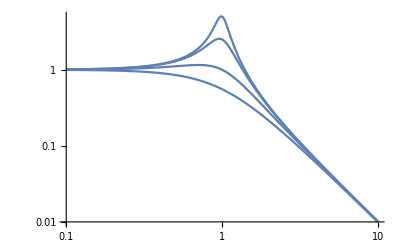

```mathematica
LogLogPlot[gmag/.ζ->{0.1,0.2,0.5,0.9},{ω,0.1,10},PlotRange->All]
```

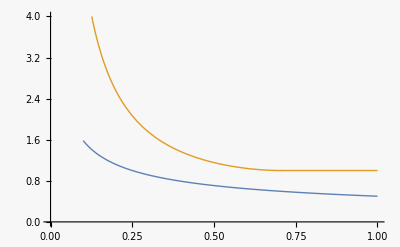

```mathematica
Plot[{1/(2 √ζ),Piecewise[{{1/(2ζ √(1-ζ^2)),ζ<1/(√2)},{1,ζ≥1/(√2)}}]},{ζ,0.1,1},PlotRange->{{0,1},{0,4}}]
```

```mathematica
{a2,b2,c2,d2}=Normal[gss]; h2=ArrayFlatten[({{a2, b2.b2ᵀ}, {-γ^-2 c2ᵀ.c2, -a2ᵀ}})]; TraditionalForm[h2]
```

(0 | 1 | 0 | 0
-1 | -2 ζ | 0 | 1
-1/γ^2 | 0 | 0 | 1
0 | 0 | -1 | 2 ζ)

```mathematica
eigs=Eigenvalues[ h2];FullSimplify[eigs,γ>0]
```

{-(√(-γ^3 (γ-2 γ ζ^2+√(1+4 γ^2 ζ^2 (-1+ζ^2)))))/γ^2,(√(γ^4 (-1+2 ζ^2)-√(γ^6+4 γ^8 ζ^2 (-1+ζ^2))))/γ^2,-√(-1+2 ζ^2+(√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ),√(-1+2 ζ^2+(√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ)}

```mathematica
e2=eigs^2;FullSimplify[e2,γ>0]
```

{2 ζ^2-(γ+√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ,2 ζ^2-(γ+√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ,-1+2 ζ^2+(√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ,-1+2 ζ^2+(√(1+4 γ^2 ζ^2 (-1+ζ^2)))/γ}

```mathematica
Simplify[e2/.ζ->0.5,γ>0]
```

{-0.5-(1. √(γ^6-0.75 γ^8))/γ^4,-0.5-(1. √(γ^6-0.75 γ^8))/γ^4,-0.5+(√(γ^6-0.75 γ^8))/γ^4,-0.5+(√(γ^6-0.75 γ^8))/γ^4}

For 1st-order system

```mathematica
g1=1/(1+ τ s); g1tf= TransferFunctionModel[g1,s]; g1ss=StateSpaceModel[g1tf]
```

-1/τ11/τ0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
p1inf=ControllabilityGramian[g1ss]; TraditionalForm[p1inf]
```

((τ Conjugate[τ])/(Conjugate[τ]+τ))

```mathematica
{a1,b1,c1,d1}=Normal[g1ss]; h1=ArrayFlatten[({{a1, b1.b1ᵀ}, {-γ^-2 c1ᵀ.c1, -a1ᵀ}})]; TraditionalForm[{a1,b1,c1,d1,h1}]
```

{(-1/τ),(1),(1/τ),(0),(-1/τ | 1
-1/(γ^2 τ^2) | 1/τ)}

```mathematica
eigs1=Eigenvalues[ h1];Simplify[eigs1,γ>0]
```

{-(√(-1+γ^2))/(γ τ),(√(-1+γ^2))/(γ τ)}